# CARBAPENEM RESISTANCE MODEL

## Data

### Preparing Directory

Clear all variables. Set directory and change setting such that when it closes it closes all outputs.

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]]}];
```

### Load Data

Reading country data on consumption and resistance and assigning them to appropriate variables.

```mathematica
countryname="US_DDD"; 
data=Import["DataSheet_cddep.xlsx",{"Data",countryname}]; (*import data*)
data = data[[All,2;;]]; 
years = data[[1]];
tt = Length[years]; 
nop = (Length[data]-6)/2; (*# of pathogens*)
isolates = data[[2;;Length[data]-5;;2]]; 
resistance = data[[3;;Length[data]-5;;2]];
rfreq =resistance/isolates; (*resistance frequency*)
carbcons =  data[[-2]]; (*CBP consumption (DDDs): total*)
conbreak = data[[-4,1;;nop]]; (*CBP consumption for PA, AB, KP, EA/C*)
cbp =data[[-3,1]]*Table[carbcons*conbreak[[i]],{i,1,nop}]; (*CBP consumption: pneumonia only & by pathogen*)
```

## Model

### Parameters & Model Structure

r(t) = frequency of resistance
k_s= natural growth rate of the sensitive strain
k_r= natural growth rate of the resistance strain (k_r < k_s)
θ = k_r-k_s< 0 
a = CBP consumption (DDD)

```mathematica
r[t_,r0_,ks_,θ_]:=ⅇ^(Total[ks*a[[1;;t]]]+θ*t)/((1/r0)-1+ⅇ^(Total[ks*a[[1;;t]]]+ θ*t));
```

### Likelihood

```mathematica
Lik[r0_,ks_,θ_]:= Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,ks,θ]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,ks,θ]],{j,1,tt}]]
```

#### Likelihood Surface

```mathematica
(*i = 3;
iso = isolates[[i]]
resis = resistance[[i]]
a = cbp[[i]]
loglik[r0_,ks_]:=Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,ks,-0.1]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,ks,-0.1]],{j,1,tt}]]
Plot3D[loglik[r0,ks],{r0,0,0.1},{ks,700,1000}]*)
```

### Model Fitting

Fit r_0 and k_s using a binomial maximum likelihood function. Fix θ based on literature.

```mathematica
θ=-0.15; (*Di Luca, 2017*)

max  = PadRight[{},nop,Null];
fr0 = max; fks=max;
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],a = cbp[[i]],{max[[i]],{fr0[[i]],fks[[i]]}}=NMaximize[{Lik[r0,ks,θ],0<r0<1},{r0,ks}, MaxIterations->100000]}]

fr0 = Table[fr0[[i]][[2]],{i,1,nop}];
fks = Table[fks[[i]][[2]],{i,1,nop}] ;

(*create table of fitted values*)
params= Join[{max},{fr0},{fks}];
headings1=Prepend[params,{"PA","KP","AB","EA/C"}];
headings2=MapThread[Prepend,{headings1,{"","Likelihood","r0","k_s"}}];
Grid[headings2,Frame-> All]
```

| PA | KP | AB | EA/C
Likelihood | -121.98 | -147.539 | -320.645 | -112.5
r0 | 0.186648 | 0.161712 | 0.0052795 | 0.000612125
k_s | 44.4629 | 194.945 | 167.571 | 322.394

### Sampling and Bayesian Melding

#### Functions

```mathematica
loglik[r0_,ks_]:=Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,ks,θ]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,ks,θ]],{j,1,tt}]];
fonGrid[x_,y_,f_]:=Module[{n,m,fvals},
n=Length[x];
m=Length[y];
fvals=Table[0,{m},{n}];(*preallocate fvals*)
Do[Do[fvals[[i,j]]=f[x[[j]],y[[i]]];,{i,1,m}];,{j,1,n}];
fvals]
(*x is an n-by-1 vector*)
(*y is an n-by-1 vector*)
(*f is a scalar function of two variables*)
(*fvals is an m-by-n matirx where fVals[[i,j]]=f[x[[j]],y[[i]]]*)

repeat[m_,n_Integer?Positive]:=Sequence@@ConstantArray[m,n]
```

#### Initialization for parameter estimates and plots

```mathematica
r0f = PadRight[{},nop,Null]; 
ksf  = PadRight[{},nop,Null]; 
lf  = PadRight[{},nop,Null];
plotD  = PadRight[{},nop,Null]; (*data*)
plotM  = PadRight[{},nop,Null]; (*model fit*)
plotS  = PadRight[{},nop,Null]; (*status quo projections*)
plotP  = PadRight[{},nop,Null]; (*intervention projections*)

nif = 0.1; (* noise around mle values for bayesian melding prior*)
nb=100; (*number of parameter values randomly selected for Bayesian melding step*)
sb=1000; (*number of weighted samples for Bayesian melding step*)
```

#### Bayesian melding for each pathogen

```mathematica
For[i=1,i<nop+1,i++,
iso = isolates[[i]];
resis = resistance[[i]];
a = cbp[[i]];

(*Take nb samples for Subscript[r, 0] and Subscript[k, s]*)
r0s = RandomReal[{(1-nif)*fr0[[i]],(1+nif)*fr0[[i]]},nb]; (*Subscript[r, 0] samples*)
kss = RandomReal[{(1-nif)*fks[[i]],(1+nif)*fks[[i]]},nb]; (*Subscript[k, s] samples*)

lik = fonGrid[r0s,kss,loglik]; (*Calculates a matrix of loglikelihood values for Subscript[r, 0], Subscript[k, s] values*)
ls = Exp[lik]; (*Exponential to get likelihood*)
w = ls/Total[Total[ls]]; (*Calculate weights for likelihood*)
lb =ArrayReshape[ls,{1,nb^2}][[1]]; (*Flatten the likelihood to get a vector*)
wb = ArrayReshape[w,{1,nb^2}][[1]]; (*Flatten the weights to get a vector*)

r0b = Table[repeat[r0s[[i]],nb],{i,1,nb}];(*Resize r0 to match likelihood vector: repeat 1st term of r0 vector n times, then 2nd term n times, etc.*)
ksb = PadRight[kss,nb^2,kss];(*Resize ks to match size of likelihood vector: repeat ks vector n times*)

ind = RandomChoice[wb->Range[nb^2],sb];(*Choose mb indices from 1 to nb^2 based on weights(importance sampling with replacement)*)
r0b = r0b[[ind]];ksb = ksb[[ind]]; lb = lb[[ind]]; (*Get posterior parameters (Subscript[r0, v],Subscript[ks, v]) and likelihood (Subscript[l, v]) based on melding*)
od = Ordering[ind];(*sort the likelihood values in order to get confidence intervals*)
r0b = r0b[[od]]; ksb=ksb[[od]];(*Order parameters in the same order as sorted likelihoods*)

r0C=r0b[[50;;1000]];ksC=ksb[[50;;1000]];(*Take the parameters corresponding 95% confidence interval of likelihoods*)
r0f[[i]] = r0C; ksf[[i]]=ksC;](*Assign 95% CI parameters for each pathogens*)
```

### Plots and Projections

#### Model fit plots

```mathematica
t=Range[1,tt]; 
pathogens = {"Pseudomonas aeruginosa","Acinetobacter baumanii","Klebsiella pneumoniae","Enterobacter aerogenes/cloacae"};

nos = Length[r0f[[1]]]; (*number of 95% CI parameters sampled*)
rm=PadRight[{},nos,Null]; (*initialize resistance from model output*)
rmins=PadRight[{},nop,Null];
rmaxs=PadRight[{},nop,Null];

For[i=1,i<nop+1,i++,
r0p =r0f[[i]];ksp = ksf[[i]]; (*save 95% CI parameters for each pathogen*)
res = Transpose@{years,rfreq[[i]]}; (*resistance frequency data*)

For[j=1,j≤nos,j++,{iso=isolates[[i]],resis = resistance[[i]],a = cbp[[i]],rm[[j]]= Table[r[k,r0p[[j]],ksp[[j]],θ],{k,1,tt}]}]; (*generate model outputs for sampled parameter sets*)
rmin = Table[Min[rm[[All,r]]],{r,1,tt}]; rmax = Table[Max[rm[[All,r]]],{r,1,tt}];(*find min and max parameter sets*)
rmins[[i]]=rmin; rmaxs[[i]]=rmax;(*store values*)

rfill = {rmin,rmax};
rfit = Table[Transpose@{years,rfill[[i]]},{i,1,2}];
plotD[[i]] = ListPlot[res,PlotStyle->{{Black,PointSize[Large]}},PlotRange->All,AxesOrigin-> {years[[1]],0}];
plotM[[i]] =ListLinePlot[Table[rfit[[j]],{j,2}],PlotStyle->RGBColor[0.75,0.75,0.75],AxesStyle->Directive[16],FrameLabel->{Year,Resistance},PlotRange->All,PlotLabel->Style[pathogens[[i]],Italic,18],Filling->{1->{2}} ,AxesOrigin-> {years[[1]],0}];]
```

#### Model projections

#### Status quo:

1. Maintain most recent consumption levels until end of projections (t_f); 
2. Maintain linear trend of increasing consumption levels until end of projections (t_f).

```mathematica
ti=years[[-1]]+1; (*projections begin at year Subscript[t, i]*)
tf =2030; (*projection until year Subscript[t, f]*) 
pyears = Range[ ti,tf]; (*vector of years from ti to tf*)
nyears = Length[pyears];(*# of years to project across*)


(*1*)
(*cbp0 = data[[-3,1]]*carbcons[[-1]]; (*current CBP consumption for pneumonia (all pathogens)*)
projSQ =ConstantArray[cbp0,Round[nyears]];
cbpSQ = Table[Join[cbp[[i]],projSQ*conbreak[[i]]],{i,1,nop}];*)

(*2*)cbpdata = Transpose@{years,carbcons}; (*CBP consumption data by year*)
lm = Normal[LinearModelFit[cbpdata,xy,xy]];
cbpmodelfit[xy_]=lm; (*linear fit for CBP consumption data*)
projSQ =cbpmodelfit[pyears]; (*status quo projection of CBP consumption (total)*)
cbpSQ = Table[Join[cbp[[i]],data[[-3,1]]*projSQ*conbreak[[i]]],{i,1,nop}];  (*CBP consumption - status quo*)
```

#### Interventions:

Start year: 2017
1. Antimicrobial reductions
	a. Formulary restrictions (immediate): 95% reduction by 2018; (intv, ey)=(0.05, 2018)
	b. Formulary restrictions (linear decrease): 95% reduction by 2020; (intv, ey)=(0.05, 2020)
	c. Stewardship (linear decrease): 22% reduction by 2020; (intv, ey)=(0.78, 2020)
2. Vaccine: 9.57% reduction by 2022; (intv, ey)=(0.9043, 2022)
3. Hand washing: 7% reduction by 2020; (intv, ey)=(0.93, 2020)

```mathematica
intv = 0.78; (*reduce current carbapenem consumption by (1-intv)% in next niy years linearly*)
ey = 2020; (*year of achieving reduction after beginning of intervention from start year*)

sy = 2017; (*beginning of intervention*)
sqyears = Range[ti,sy-1];  (*array of status quo years prior to intervention start*)
ncy =Length[sqyears]; (*no of status quo years before beginning of intervention*)
niy = ey-sy+1; (*no of intervention years*)

(*create array for future CBP consumption*)
(*1*)(*projI =Join[ConstantArray[cbp0,Round[ncy]],Range[cbp0,intv*cbp0,cbp0*(intv-1)/(niy-1)],ConstantArray[intv*cbp0,Round[nyears-ncy-niy]]];*)

(*2*)
projI =Join[cbpmodelfit[sqyears],Range[cbpmodelfit[sqyears][[-1]],intv*cbpmodelfit[sqyears][[-1]],cbpmodelfit[sqyears][[-1]]*(intv-1)/(niy-1)],ConstantArray[intv*cbpmodelfit[sqyears][[-1]],Round[nyears-ncy-niy]]]; (*intervention projection of CBP consumption (total)*)
cbpI = Table[Join[cbp[[i]],data[[-3,1]]* projI*conbreak[[i]]],{i,1,nop}]; (*CBP consumption - intervention*)
```

#### Projected resistance frequencies:

```mathematica
(*initalize stored values*)
rSQ =PadRight[{},nos,Null]; (*resistance projections for status quo*)
rSQms=PadRight[{},nop,Null]; rSQMs=PadRight[{},nop,Null];  
rI=PadRight[{},nos,Null];(*resistance projections for intervention*)
rIms=PadRight[{},nop,Null]; rIMs=PadRight[{},nop,Null]; 

For[i=1,i<nop+1,i++,
r0p =r0f[[i]];ksp = ksf[[i]];(*save 95% CI parameters for each pathogen*)
res = Transpose@{years,rfreq[[i]]}; (*resistance frequency data*)

(*status quo projections*)
For[j=1,j≤nos,j++,{iso=isolates[[i]],resis = resistance[[i]],a = cbpSQ[[i]],rSQ[[j]]= Table[r[k,r0p[[j]], ksp[[j]],θ],{k,tt,tt+nyears}]}];
rSQm = Table[Min[rSQ[[All,r]]],{r,1,nyears+1}]; rSQM = Table[Max[rSQ[[All,r]]],{r,1,nyears+1}]; (*generate model outputs for sampled parameter sets*)
rSQms[[i]]=rSQm[[2;;All]]; rSQMs[[i]]=rSQM[[2;;All]];(*store values (status quo)*)
rSQfill = {rSQm,rSQM};


(*intervention projections*)
For[j=1,j≤nos,j++,{iso=isolates[[i]],resis = resistance[[i]],a = cbpI[[i]],rI[[j]]= Table[r[k,r0p[[j]],ksp[[j]],θ],{k,tt,tt+nyears}]}];
rIm = Table[Min[rI[[All,r]]],{r,1,nyears+1}]; rIM = Table[Max[rI[[All,r]]],{r,1,nyears+1}]; (*generate model outputs for sampled parameter sets*)
rIms[[i]]=rIm[[2;;All]]; rIMs[[i]]=rIM[[2;;All]];(*store values (status quo)*)
rIfill = {rIm,rIM};

(*plots*)
ploty=Range[years[[-1]],tf];
fitS = Table[Transpose@{ploty,rSQfill[[i]]},{i,1,2}];
fitP = Table[Transpose@{ploty,rIfill[[i]]},{i,1,2}];
plotS[[i]] =ListLinePlot[Table[fitS[[j]],{j,2}],PlotStyle->{RGBColor[0.75,0.75,0.75]},FrameLabel->{{x,Year},{y,Resistance}},PlotRange->All,Filling->{1->{2}},AxesOrigin-> {years[[1]],0}];
plotP[[i]] =ListLinePlot[Table[fitP[[j]],{j,2}],PlotStyle->RGBColor[0.3,0.5,0.75],FrameLabel->{{x,Year},{y,Resistance}},PlotLabel->"KP",PlotRange->All,Filling->{1->{2}},AxesOrigin-> {years[[1]],0}];]
```

#### Projected Plots

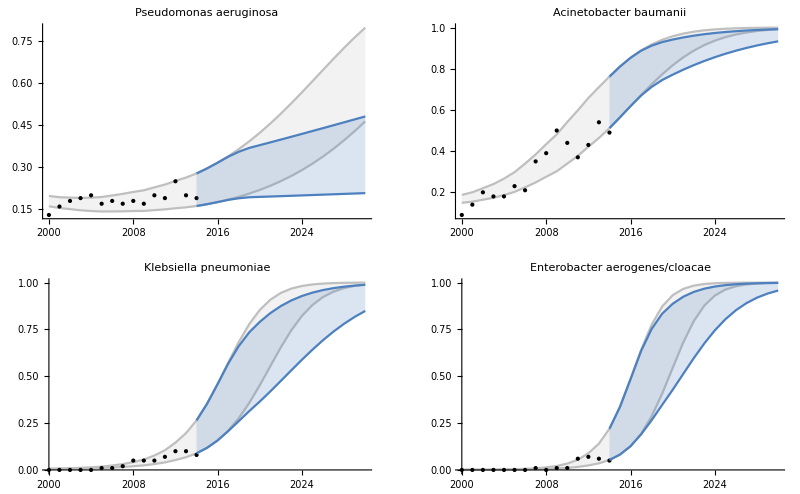
-Graphics-Stewardship(22% reduction in consumption by 2020)Resistance frequencyYears

```mathematica
title="Stewardship(22% reduction in consumption by 2020)";
(*Export["Intervention_05.png",plots];*)

plots =Panel[GraphicsGrid[{{Show[plotM[[1]],plotD[[1]],plotS[[1]],plotP[[1]],PlotRange->All],Show[plotM[[2]],plotD[[2]],plotS[[2]],plotP[[2]],PlotRange->All,Axes->True,AxesOrigin->{2000,0.05}]},{Show[plotM[[3]],plotD[[3]],plotS[[3]],plotP[[3]],PlotRange->All],Show[plotM[[4]],plotD[[4]],plotS[[4]],plotP[[4]],PlotRange->All]}},ImageSize->Full],{Style[title,"Panel",28,Background->White],Style[Rotate["Resistance frequency",90 Degree],"Panel",24,Background->White],Style["Years","Panel",24,Background->White]},{{Top,Center},{Left,Center},{Bottom,Center}},Appearance->"Frameless",Background->White]
```

# Economic & Health Outcomes

### Mortality

```mathematica
rSQms[[3]]
```

{0.118059,0.157526,0.209545,0.276139,0.357822,0.452377,0.554182,0.655008,0.746411,0.822429,0.880914,0.923028,0.951765,0.970549,0.982414,0.989703}

```mathematica
np=data[[-1]][[-1]]*conbreak*0.11055; (*# pneumonia patients prescribed CBPs by pathogen*)

(*carbapenem prescription breakdown for KPC*)
kp={20/105,19/105,29/105,35/105}; (*carbapenem monotherapy, carbapenem combination therapy, sparing mono, sparing combo*)

(*associated mortality rates*)
kpm={{0.467,0.278,0.467,0.304},{0.234,0.234,0.234,0.234}}; (*resistant/susceptible: carbapenem monotherapy, carbapenem combination therapy, sparing mono, sparing combo*)
```

```mathematica
(*STATUS QUO:  kp # of deaths*)
mSQm=Total[np[[3]]*(rSQms[[3]]*(kp[[1]]*kpm[[1]][[1]] + kp[[2]]*kpm[[1]][[2]]) + (1-rSQms[[3]])*(kp[[1]]*kpm[[2]][[1]] + kp[[2]] *kpm[[2]][[2]]))]
mSQM=Total[np[[3]]*(rSQMs[[3]]*(kp[[1]]*kpm[[1]][[1]] + kp[[2]]*kpm[[1]][[2]]) + (1-rSQMs[[3]])*(kp[[1]]*kpm[[2]][[1]] + kp[[2]] *kpm[[2]][[2]]))]
```

32071.9

35078.8

```mathematica
(*INTERVENTION: kp # of deaths*)
mIm=intv*mSQm+ Total[ (1-intv)*np[[3]]*((rIms[[3]]*(kp[[3]]*kpm[[1]][[3]] + kp[[4]]*kpm[[1]][[4]]) + (1-rIms[[3]])*(kp[[3]]*kpm[[2]][[3]] + kp[[4]] *kpm[[2]][[4]])))]

mIM=intv*mSQM +Total[(1-intv)*np[[3]]*((rIMs[[3]]*(kp[[3]]*kpm[[1]][[3]] + kp[[4]]*kpm[[1]][[4]]) + (1-rIMs[[3]])*(kp[[3]]*kpm[[2]][[3]] + kp[[4]] *kpm[[2]][[4]])))]
```

35986.5

39939.1

### Length of Stay

```mathematica
(*Length of stay*)
rlos=5; (*resistant*)
slos=2; (*sensitive*)
wardcost=2877;  (*general ward cost/day*)
```

```mathematica
(*kp general ward costs*)
kplos[r_]:=ipp[[1]]*wardcost*((rlos*((r*(kp[[1]]+kp[[2]]))+(1-r)*(kp[[3]]+kp[[4]])))+(slos*(r*(kp[[3]]*kp[[4]])+((1-r)*(kp[[1]]+kp[[2]])))));
Apply[kplos,{{z[[1]]}}]
```

Part::partd: Part specification z⟦1⟧ is longer than depth of object.

Part::partd: Part specification ipp⟦1⟧ is longer than depth of object.

{2877 ipp⟦1⟧ (2 (13/35 (1-z⟦1⟧)+(29 z⟦1⟧)/315)+5 (64/105 (1-z⟦1⟧)+(13 z⟦1⟧)/35))}